```mathematica
ClearAll[Evaluate[Context[]<>"*"]]
```

```mathematica
Needs["Spline`"];Needs["Representation`"];
```

```mathematica
spline1s={0.01,0.01};
spline1e={1.99,0.01};
midpoint = {1.01,0.8};
```

```mathematica
InverseRepresentation[Repr=Representation[spline1s,midpoint,spline1e];Repr[[1]],Repr[spline1s,midpoint,spline1e][[2]],Repr[spline1s,midpoint,spline1e][[3]]]
```

{{0.211924,1.06567},{0.81345,0.209551},{2.59248,0.27322}}

```mathematica
DynamicModule[{s=spline1s,c2=midpoint,e=spline1e},{Graphics[{Dynamic[Line[Repr=Representation[s,c2,e];InvRepr=InverseRepresentation[Repr[[1]],Repr[[2]],Repr[[3]]];InvRepr]],Locator[Dynamic[s]],Locator[Dynamic[c2]],Locator[Dynamic[e]]},PlotRange->2]}]
```

```mathematica
DynamicModule[{s=spline1s,c2=midpoint,e=spline1e},{Graphics[{Dynamic[Line[{{Repr=Representation[s,c2,e];Repr[[1]],Repr[[2]],Repr[[2]],Repr[[3]]}}]],Locator[Dynamic[s]],Locator[Dynamic[c2]],Locator[Dynamic[e]]},PlotRange->2]}]
```

```mathematica
DynamicModule[{s=spline1s,c2=midpoint,e=spline1e},{Graphics[{Dynamic[Point[arc[s,c2,e]]],Locator[Dynamic[s]],Locator[Dynamic[c2]],Locator[Dynamic[e]]},PlotRange->2]}]
```

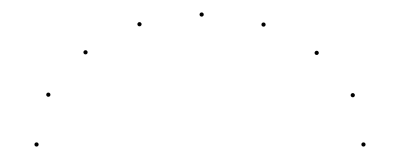

```mathematica
Graphics[{Point[arc[spline1s,midpoint,spline1e]]}]
```